```mathematica
(*for plotting*)
On[Assert];
th = 1.75; asz =20;
```

```mathematica
(*CONSTANTS AND SIMPLE FUNCTIONS USED*)

(*Convection*)
cp =29.3; (*J/ mol K*)
wind = 1; (*m/s*)
(*original data tissue density:
1 kg /l =  1 kg/dm^3 = 1000g/dm^3 = 1000 g/ 10^(-3) m^3  = 1 10^6 g/m^3
*)
δ = 0.15 10^(6);(*measurement gives the 0.15. g/m^3*)
Ksth =0.05* cp (*this is tissue conductance. A sleeping bag has 0.05 (ex #6.4, mol / m2 s * J / mol K  *);

s = 3.3472 ;(*specific heat capacity, 0.8 cal /g C = 0.8*4.184 J/g C*)
σ=5.67 10^(-8);(*W/m2 K4 = J / m2 s K*)
e = 0.04184;(*energy per contraction: 0.01 cal/g = 0.01*4.184 j/g*)

Kv[z_]:= cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (* J/mol K x mol /m2 s = J / m2 K s*);

aw = 0.25; (*something per second*)
f[T_]:= aw T;

(*Start from radius calculating it is easier *)
rad[z_]:= (3. z/(2 π δ))^(1/3);
ch = 1; (*ch is the proportion of the cap with respect to the radius. radius * ch gives the height*)
h[z_]:= rad[z]* ch; (*The height of the cap*) 

(*ratio between thoracic and total mass*)
(*fcz[z_] := ((1/(3 2)) π h[z]^2  (3 rad[z] - h[z]))/(2/3 π r^3);*)
fcz[z_] := 0.5;(*((1/4)  h[z]^2  (3 rad[z] - h[z]))/(rad[z]^3);*)

(*Total surface of the spherical cap = surface of the thorax*)
Ath[z_]:= π rad[z] h[z] +  2 rad[z]^2 ArcCos[(rad[z]- h[z])/rad[z]] - (rad[z]-h[z])Sqrt[2 rad[z] h[z] - h[z]^2](*the first part is divided by 2 because of half a sphere, from pytagorian the base is a = (h (2 r - h))^(1/2) note that *)

(*Total surface are of  rest *)
As[z_]:= ( 2 π rad[z]^2  -  π rad[z] h[z] )  +   π rad[z]^2 (* m2*);
```

## Main code for minimum temperature for warm-up

```mathematica
SR  = #/(6*3600) *0.25 1320. &;
Te = #2 + 0 #1/(6*3600.) &;  

(*this function is for the change in thoracic (and surface) temperature *)
changeTth[z_, rK1_, rK2_,minT_,free_]:= Module[{maxt = 6*3600, ε= 0.95, r3 =0.5,sol, cz = fcz[z]},
Assert[cz<0.75];
sol = If[free == 0,
NDSolve[
{ Tth'[t] == 1/(s cz z ) (0. * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz)z) *( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  0.05(Ts[t]- Te[t,minT])^(1.25) (1/(z/δ))^(1/12) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,minT])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==minT},{Tth,Ts},{t,0,maxt}],
NDSolve[
{Tth'[t] == 1/(s cz z) (0. * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz) z) * ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (Ts[t]- Te[t,minT]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,minT])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==minT},{Tth,Ts},{t,0,maxt}]
];
sol];

(*This finds an interval of temperature such that at maxt, f(T1) < Tw and f(T2)>Tw, the condition is that Abs[f(t1) - f(t2)] < 0.01*)
findTmin[z_, rK1_, rK2_, free_]:=Module[{Tw = 28 + 1. 0.75 z,T1,T2, Tmid,maxt = 6*3600,Tf1,Tf2,sol,Tfmid},
T1 = 0;
T2 = 100;
Tf1 = 0;
Tf2 = 100; 
Tmid = T1;

sol  = changeTth[z,rK1, rK2, T1, free];
Tf1 = Tth[maxt]/.sol[[1]];
If[Tf1 > Tw, Goto[end]];

While[Abs[Tf1 -Tf2] > 10^(-2),
Tmid = T1 + (T2 - T1 )/2;

sol  = changeTth[z,rK1, rK2, Tmid, free];
Tfmid = Tth[maxt]/.sol[[1]];

Which[
Tfmid < Tw,Tf1 = Tfmid;T1 = Tmid,
Tfmid > Tw,Tf2 = Tfmid;T2 = Tmid,
Tfmid == Tw,T1 = Tmid;Goto[end] 
];
];
Label[end];
N@{z,T1}];
```

### This is for free convection

```mathematica
vect = Flatten[{Range[0.001,0.01,0.001],Range[0.02,0.1,0.01],Range[0.2,2,0.1],Range[3,10,1]}];

(*This is for free convection*)
case = 0; 
rK1 = 1;
(*!!!! Don't forget to change the slope for SR for each run, here it is 0.25 !!!!*)
data1= Table[Table[findTmin[z,rK1,rK2,case], {z, vect}],{rK2,{0.1,1,10}}];
rK1 = 0.1;
(*!!!! Don't forget to change the slope for SR for each run, here it is 0.25 !!!!*)
data2= Table[Table[findTmin[z,rK1,rK2,case], {z, vect}],{rK2,{0.1,1,10}}];
```

$Aborted

```mathematica
d1 = ListLogLinearPlot[data1,Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Red,AbsoluteThickness[th]}, {Black,AbsoluteThickness[th]},{Blue,AbsoluteThickness[th]}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium,PlotRangePadding->None];
d2 = ListLogLinearPlot[data2,Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Red,AbsoluteThickness[th]}, {Black,AbsoluteThickness[th]},{Blue,AbsoluteThickness[th]}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium,PlotRangePadding->None];
```

```mathematica
Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\ms_fig\\fig2a.jpg",d1, ImageResolution->100];
Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\ms_fig\\fig2b.jpg",d2, ImageResolution->100];
```

### This is for laminar convection

```mathematica
vect = Flatten[{Range[0.001,0.01,0.001],Range[0.02,0.1,0.01],Range[0.2,2,0.1],Range[3,10,1]}];

(*This is for laminar convection*)
case = 1; 
rK1 = 1;
(*!!!! Don't forget to change the slope for SR for each run, here it is 0.25 !!!!*)
data1= Table[Table[findTmin[z,rK1,  rK2,case], {z, vect}],{rK2,{0.1,1,10}}];
rK1 = 0.1;
(*!!!! Don't forget to change the slope for SR for each run, here it is 0.25 !!!!*)
data2= Table[Table[findTmin[z,rK1,rK2,case], {z, vect}],{rK2,{0.1,1,10}}];
```

```mathematica
d1 = ListLogLinearPlot[data1,Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Red,AbsoluteThickness[th]}, {Black,AbsoluteThickness[th]},{Blue,AbsoluteThickness[th]}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium,PlotRangePadding->None];
d2 = ListLogLinearPlot[data2,Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Red,AbsoluteThickness[th]}, {Black,AbsoluteThickness[th]},{Blue,AbsoluteThickness[th]}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium,PlotRangePadding->None];
```

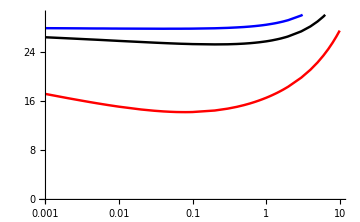

```mathematica
d2
```

```mathematica
Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\ms_fig\\fig2c.jpg",d1, ImageResolution->100];
Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\ms_fig\\fig2d.jpg",d2, ImageResolution->100];
```

### This is for laminar convection, NSF fig

```mathematica
vect = Flatten[{Range[0.001,0.01,0.001],Range[0.01,0.1,0.01],Range[0.2,2,0.1],Range[3,10,1]}];

(*This is for laminar convection*)
case = 1; 
rK1 = 1;
(*!!!! Don't forget to change the slope for SR for each run, here it is 0.25 !!!!*)
data1= Table[Table[findTmin[z,rK1,  rK2,case], {z, vect}],{rK2,{0.1,5}}];
```

```mathematica
as = Directive[AbsoluteThickness[th-1],fs,Black,FontFamily->"Arial"];
```

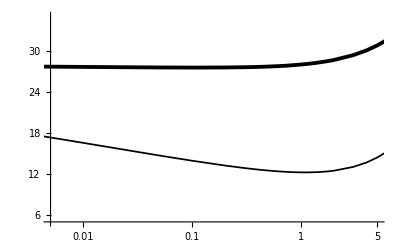

```mathematica
d1 = ListLogLinearPlot[data1,Joined->True,PlotRange-> {{0.005,5}, {5,35}},PlotStyle->{{Black,AbsoluteThickness[th-0.5]}, {Black,AbsoluteThickness[th+1]}},AxesStyle->as,PlotRangePadding->None,Ticks->{{0.01,0.1,1,5},All}]
```

```mathematica
Export["C:\\Users\\Tanjona\\Documents\\Projects\\NSF_IEP\\fig2a.pdf",d1];
```

### This works for all analyses, if aw = 0 then it becomes ectothermic

```mathematica
SR  = #/(6*3600) *cSR 1320. &;
Te = #2 + 0 #1/(6*3600.) &;  

(*this function is for the change in thoracic (and surface) temperature *)
changeTthEndo[z_, rK1_, rK2_,minT_,free_,aw_]:= Module[{maxt = 6*3600, ε= 0.95, r3 =0.5,sol, cz = fcz[z]},
Assert[cz<0.75];
sol = If[free == 0,
NDSolve[
{ Tth'[t] == 1/(s cz z ) (aw * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz)z) *( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  0.05Min[0.,(Ts[t]- Te[t,minT])]^(1.25) (1/(z/δ))^(1/12) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,minT])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==minT},{Tth,Ts},{t,0,maxt}],
NDSolve[
{Tth'[t] == 1/(s cz z) (aw * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz) z) * ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (Ts[t]- Te[t,minT]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,minT])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==minT},{Tth,Ts},{t,0,maxt}]
];
sol];

(*This finds an interval of temperature such that at maxt, f(T1) < Tw and f(T2)>Tw, the condition is that Abs[f(t1) - f(t2)] < 0.01*)
findTminEndo[z_, rK1_, rK2_, free_,aw_]:=Module[{Tw = 28 + 1. 0.75 z,T1,T2, Tmid,maxt = 6*3600,Tf1,Tf2,sol,Tfmid},
T1 = 0;
T2 = 100;
Tf1 = 0;
Tf2 = 100; 
Tmid = T1;

sol  = changeTthEndo[z,rK1, rK2, T1, free,aw];
Tf1 = Tth[maxt]/.sol[[1]];
If[Tf1 > Tw, Goto[end]];

While[Abs[Tf1 -Tf2] > 10^(-2),
Tmid = T1 + (T2 - T1 )/2;

sol  = changeTthEndo[z,rK1, rK2, Tmid, free,aw];
Tfmid = Tth[maxt]/.sol[[1]];

Which[
Tfmid < Tw,Tf1 = Tfmid;T1 = Tmid,
Tfmid > Tw,Tf2 = Tfmid;T2 = Tmid,
Tfmid == Tw,T1 = Tmid;Goto[end] 
];
];
Label[end];
N@{z,T1}];
```

```mathematica
(* !!! don't forget to change the slope of solar radiation !!!*)
vect = Flatten[{Range[0.001,0.01,0.001],Range[0.02,0.1,0.01],Range[0.2,2,0.1],Range[3,10,1]}];

Do[
SR  = #/(6*3600) *cSR 1320. &;
Te = #2 + 0 #1/(6*3600.) &;  

DATA= {1,2};
Do[
data= Table[Table[findTminEndo[z,rK1,rK2,case-1,aw], {z, vect}],{rK1,{0.1,1,10}},{rK2,{0.1,1,10}}];
DATA[[case]] = data;
,{case,{1,2}}];

fig = {};
Do[
d1 = ListLogLinearPlot[DATA[[case,1]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d2 = ListLogLinearPlot[DATA[[case,2]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d3 = ListLogLinearPlot[DATA[[case,3]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
AppendTo[fig,{d1,d2,d3}];
,{case,{1,2}}];
out =GraphicsGrid[Transpose[fig],ImageSize->Large];
Export["C:\\Users\\Tanjona\\Documents\\energy_budget\\analyses_fig\\warm-up\\fig_warm-up_cSR_"<>ToString@cSR<>"_aw_"<>ToString@aw<>".jpeg",out,ImageResolution-> 100];
,{aw, {0.5,1}},{cSR ,{ 0.25,0.5,1}}]//AbsoluteTiming
```

{151.17723,Null}

```mathematica
100
```

## Here I plot warm-up time

```mathematica
On[Assert];

(*Position of the sun in the sky as a function of day of the year, time of the day, and latitude at longitude = 0*)
SolarRadiation[J_,t_,ϕ_]:= Module[{result,S0=1.361,sinδ,δ,cosδ, cosψ,sol,trise,tset,tt, DtoR = π/180,hs},
sinδ = 0.39785 Sin[(278.97 + 0.9856 J + 1.9165 Sin[(356.6 + 0.9856 J)DtoR])DtoR];
(*this is solar declination*)
δ = ArcSin[sinδ];
cosδ = Cos[δ];
cosψ[ti_]:=Sin[ϕ DtoR]sinδ + Cos[ϕ DtoR] cosδ Cos[(15.(ti-12))DtoR];

hs[δ_]:= ArcCos[(0 - Sin[ϕ DtoR]sinδ)/(Cos[ϕ DtoR] cosδ)]1/DtoR; 
(*cosψ disapears because we use geometric sunset*)
trise = 12- hs[δ]/15;
tset = 12 + hs[δ]/15;

If[t< trise || t > tset, 
result = 0,
result = S0 cosψ[t];
];
result *= 1000;
result];

(*Position of the sun in the sky as a function of day of the year, time of the day, and latitude at longitude = 0*)
SunRise[J_,ϕ_]:= Module[{result,sinδ,δ,cosδ, cosψ,sol,trise,tset,tt, DtoR = π/180,hs},
sinδ = 0.39785 Sin[(278.97 + 0.9856 J + 1.9165 Sin[(356.6 + 0.9856 J)DtoR])DtoR];
(*this is solar declination*)
δ = ArcSin[sinδ];
cosδ = Cos[δ];

hs[δ_]:= ArcCos[(0 - Sin[ϕ DtoR]sinδ)/(Cos[ϕ DtoR] cosδ)]1/DtoR; 
(*cosψ disapears because we use geometric sunset*)
trise = 12- hs[δ]/15;
result= Re@trise;
result];

(*Fixed constant and solar radiation function *)
day = 72; lat = 30 ;
trise = SunRise[day,lat];ZZ= {0.01,0.1,1,10};

(* data for solar radiation *)
predata = Table[{t, SolarRadiation[day,t,lat]},{t, trise,trise+12,12/10}];
SR = Interpolation[predata];

th = 1.75; fs  =24;

ps = {{Gray,AbsoluteThickness[th]},{Dashed,Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[2 th]}};

as = Directive[AbsoluteThickness[th],fs,Black,FontFamily->"Arial"];

(*CONSTANTS AND SIMPLE FUNCTIONS USED*)

Ek =  7541; (*This is the ratio between E and k*)
c0= 28.;
c1 = 1.5;
cz = 0.5;

(*Convection*)
cp =29.3; (*J/ mol K*)
wind = 1; (*m/s*)
(*original data tissue density:
1 kg /l =  1 kg/dm^3 = 1000g/dm^3 = 1000 g/ 10^(-3) m^3  = 1 10^6 g/m^3
*)
δ = 0.15 10^(6);(*measurement gives the 0.15. g/m^3*)
Ksth =0.05* cp (*this is tissue conductance. A sleeping bag has 0.05 (ex #6.4, mol / m2 s * J / mol K  *);

s = 3.3472 ;(*specific heat capacity, 0.8 cal /g C = 0.8*4.184 J/g C*)
σ=5.67 10^(-8);(*W/m2 K4 = J / m2 s K*)
e = 0.04184;(*energy per contraction: 0.01 cal/g = 0.01*4.184 j/g*)

rK1 = 1; (* Coefficient for the conductance between the thorax and the rest of the body *)
rK2 = 1; (* Coefficient for the convection between the thorax and the environment *)
free = 0; (* Binary value 0 or 1 where there is free convection or laminar convection*)

Kv[z_]:= cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (* J/mol K x mol /m2 s = J / m2 K s*);

aw = 0.25; (*something per second*)
f[T_]:= aw T;

(*Start from radius calculating it is easier *)
rad[z_]:= (3. z/(2 π δ))^(1/3);
ch = 1; (*ch is the proportion of the cap with respect to the radius. radius * ch gives the height*)
h[z_]:= rad[z]* ch; (*The height of the cap*) 

(*ratio between thoracic and total mass*)
(*fcz[z_] := ((1/(3 2)) π h[z]^2  (3 rad[z] - h[z]))/(2/3 π r^3);*)
fcz[z_] := ((1/4)  h[z]^2  (3 rad[z] - h[z]))/(rad[z]^3);

(*Total surface of the spherical cap = surface of the thorax*)
Ath[z_]:= π rad[z] h[z] +  2 rad[z]^2 ArcCos[(rad[z]- h[z])/rad[z]] - (rad[z]-h[z])Sqrt[2 rad[z] h[z] - h[z]^2](*the first part is divided by 2 because of half a sphere, from pytagorian the base is a = (h (2 r - h))^(1/2) note that *)

(*Total surface are of  rest *)
As[z_]:= ( 2 π rad[z]^2  -  π rad[z] h[z] )  +   π rad[z]^2 (* m2*);

(*function for changes in environmental temperature*)
fTemp[t_,trise_,Trise_,Tmax_]:= Module[{tmax,tset,Tnoon,Tset,cT = 0.5,result},

If[
Trise == Tmax,result = Trise;Goto["end"]
];
Assert[Tmax >Trise];

tmax = 12 + 0.5 (12 - trise);
tset = 12 + (12- trise);
Tnoon  = Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) 12;
Tset = Tnoon + cT (Tmax - Tnoon);

result = 
Which[
trise≤ t< tmax,
 Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) t,
tmax ≤ t< tset,
 Tmax - (Tset- Tmax)/(tset - tmax) tmax+ (Tset- Tmax)/(tset - tmax) t,
tset ≤ t< trise +24,
 Tset  - (Trise - Tset)/(trise +24  - tset) tset + (Trise - Tset)/(trise +24  - tset)t
];

Label["end"];

result];

(*this function solve the the change in thoracic (and surface) temperature and find the warm-up time *)
Wtime[z_, rK1_, rK2_,starttf_,endtf_,free_, trise_, Trise_, Tmax_]:= Module[{ ε= 0.95, r3 =0.5,sol, cz = fcz[z], T1 , xy,pos,result, activetemp = c0 + c1 z cz ,Temp, newendtf, yy,maxyy,t1,t2,yt1,yt2,tmid,ytmid},

Temp[t_]:= fTemp[t,trise,Trise, Trise + Tmax ]; (*Simplify the definition of changes in temperature*)

T1 = Temp[starttf];
Assert[NumericQ@T1 == True];
newendtf = Min[endtf,12  +  (12 -trise)];

If[T1 ≥ activetemp, result = 0.; Goto[end]];

sol = If[free == 0,
NDSolve[
{ Tth'[t] == 1/(s cz z ) (0. * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz)z) *( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  0.05Max[0,(Ts[t]- Temp[t/3600.])]^(1.25) (1/(z/δ))^(1/12) - σ ε (273 + Ts[t])^4 + σ ε (273 + Temp[t/3600.])^4 + r3  SR[t/3600.])) ,Tth[starttf*3600.]==Ts[starttf*3600.]==T1},{Tth,Ts},{t,starttf *3600., newendtf* 3600.}],
NDSolve[
{Tth'[t] == 1/(s cz z) (0. * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz) z) * ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (Ts[t]- Temp[t/3600.]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Temp[t/3600.])^4 + r3 SR[t/3600.])) ,Tth[starttf*3600.]==Ts[starttf*3600.]==T1},{Tth,Ts},{t,starttf *3600.,newendtf *3600.}]
];


(* Compute all values *)
yy = Table[Evaluate[Re@Tth[t]/.sol],{t,starttf*3600,newendtf*3600,2}];
maxyy = Max[yy];

If[maxyy < activetemp,
result = endtf -starttf,
pos = Position[yy,maxyy][[1,1]];
t1 = starttf*3600;
t2 = t1 + 2(pos-1); (*The minus one occurs because imagine max is at starttf, time 2 because of discretization in yy*)
yt1 = Evaluate[Re@Tth[t1] /. sol][[1]] - activetemp;
yt2 = Evaluate[Re@Tth[t2] /. sol][[1]] -activetemp;
Assert[yt1*yt2 < 0];
While[Abs[yt1 -yt2] > 10^(-5),
tmid = t1 + (t2 -t1)/2;
ytmid = Evaluate[Re@Tth[tmid] /. sol][[1]] - activetemp;
If[ytmid < 0,
t1 = tmid;
yt1 = ytmid,
t2 = tmid;
yt2 = ytmid
];
];
result = (t1 + t2)/(2. 3600) - starttf;
];
Label[end];
result];
```

### This is for free convection

```mathematica
vect = Flatten[{Range[0.001,0.01,0.001],Range[0.02,0.1,0.01],Range[0.2,2,0.1],Range[3,10,1]}];
```

```mathematica
free = 0;
data1 = Table[Table[{z,Wtime[z, rK1,1,trise,12 + (12 - trise),free, trise, 20,20]},{z,vect}],{rK1,{1,0.1}}];
data2 = Table[Table[{z,Wtime[z, rK1,1,trise+3,12 + (12 - trise),free, trise, 20,20]},{z,vect}],{rK1,{1,0.1}}];
```

```mathematica
d1 = ListPlot[data1,Joined->True,PlotRange-> {{0,5}, All},PlotStyle->{{Blue,AbsoluteThickness[th-1]}, {Blue,AbsoluteThickness[th+1]}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium,PlotRangePadding->None];

d2 = ListPlot[data2,Joined->True,PlotRange-> {{0,5}, All},PlotStyle->{{Red, AbsoluteThickness[th-1]}, {Red,AbsoluteThickness[th+1]}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium,PlotRangePadding->None];
```

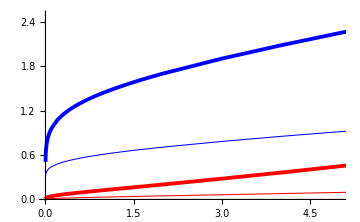

```mathematica
d3 =Show[d1,d2,PlotRange-> {{0,5},{0,2.5}}]
Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\ms_fig\\fig3a.jpg",d3, ImageResolution->100];
```

### This is for laminar convection

```mathematica
vect = Flatten[{Range[0.001,0.01,0.001],Range[0.02,0.1,0.01],Range[0.2,2,0.1],Range[3,10,1]}];
```

```mathematica
free = 1;
data1 = Table[Table[{z,Wtime[z, rK1,1,trise,12 + (12 - trise),free, trise, 20,20]},{z,vect}],{rK1,{1,0.1}}];
data2 = Table[Table[{z,Wtime[z, rK1,1,trise+3,12 + (12 - trise),free, trise, 20,20]},{z,vect}],{rK1,{1,0.1}}];
```

```mathematica
d1 = ListPlot[data1,Joined->True,PlotRange-> {{0,5}, All},PlotStyle->{{Blue,AbsoluteThickness[th-1]}, {Blue,AbsoluteThickness[th+1]}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium,PlotRangePadding->None];

d2 = ListPlot[data2,Joined->True,PlotRange-> {{0,5}, All},PlotStyle->{{Red, AbsoluteThickness[th-1]}, {Red,AbsoluteThickness[th+1]}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium,PlotRangePadding->None];
```

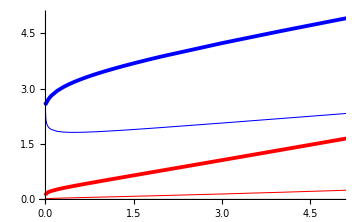

```mathematica
d3 =Show[d1,d2,PlotRange-> {{0,5},{0,5}}]
Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\ms_fig\\fig3b.jpg",d3, ImageResolution->100];
```

### This is for endothermic wam-up